```mathematica
(*USER ACTION REQUIRED

Write down the name of the experiment. The directory where this notebook is saved must contain a file of the form name<>"hypercloud.mx" previously produced by the HypercloudExtractor notebook*)
name="DemoExperiment"(*"SyntheticLogSpiral"*);


(*USER CHOICE
Choose below if you want to use the version of the training with penalties or without. Choose between "NoPenalty", "P1", or "P1_P2"*)
pen="P1_P2";



(*USER CHOICE
Choose below if you want to have a full-length training routine ("Long") or a quick preview ("Quick"). If set to "Long", then the training will involve 1M iterations for stage 1, 900k iterations for stage 2 and 100k iterations for stage 3. If set to "Quick", these stages will be reduced to 500k, 500k and 50k, respectively *)
trainingschedule="Long";



SetDirectory[NotebookDirectory[]];


(*This If treats the synthetic dataset "SyntheticLogSpiral.dat" provided in the github repository differently because it's a .dat file and because it is not split into different scans, so we only have hypercloudflat object, not hypercloud object (with scans separated). The rest of the notebook makes no reference to hypercloud, so hypercloudflat is sufficient. But we still need information about the time each scan took for the purposes of rescaling and generating output. *)
If[name=="SyntheticLogSpiral",

hypercloudflat=Import[NotebookDirectory[]<>"SyntheticLogSpiral.dat"];
timepscan=8/20;
radius=1;

,

Get[NotebookDirectory[]<>name<>"hypercloud.mx"];
Clear[hypercloudraw];
timepscan=fpscan/camerafps;



(*Sometimes the scans at the top of the tank contain a few times higher number of data points than the scans at the bottom of the tank which may cause imbalanced weighing of the fit. This line decimates the data from each scan such that the number of points is roughly equal in each scan. In this case 50000 points is the target and if the datasets are smaller, then the dataset is not decimated.

Feel free to comment out this line or change the 50000 with a different number. We observed that on some hardware, choosing a much larger number than 50k may result in a crash when constructing the alpha shape of the latent space. *)

hypercloud=Table[hypercloud[[i,1;;-1;;Max[Round[Length[hypercloud[[i]]]/50000],1]]],{i,Length@hypercloud}];
hypercloudflat=Flatten[hypercloud,1];

]



(*This estimates the translational motion of the object and represents it as a 5th order polynomial. Feel free to add or remove terms if you wish.*)

xtranslation=GeneralizedLinearModelFit[hypercloudflat[[All,{4,1}]],{1,scan,scan^2,scan^3,scan^4,scan^5},scan]["Function"]
ytranslation=GeneralizedLinearModelFit[hypercloudflat[[All,{4,2}]],{1,scan,scan^2,scan^3,scan^4,scan^5},scan]["Function"]
ztranslation=GeneralizedLinearModelFit[hypercloudflat[[All,{4,3}]],{1,scan,scan^2,scan^3,scan^4,scan^5},scan]["Function"]

(*This line creates a set of clouds with the removed mean translational component. This will be reversed after training when producing the output*)
cloudaux={#[[1]]-xtranslation[#[[4]]],#[[2]]-ytranslation[#[[4]]],(#[[3]]-ztranslation[#[[4]]]),#[[4]]}&/@hypercloudflat;
```

0.0140714+4.20232×10^-6 #1-3.25641×10^-8 #1^2-2.38531×10^-10 #1^3+1.03585×10^-12 #1^4-9.97193×10^-16 #1^5&

0.00312059+0.0000210657 #1-2.60489×10^-7 #1^2+8.68357×10^-10 #1^3-1.12165×10^-12 #1^4+5.58785×10^-16 #1^5&

-0.155907-0.00039116 #1+1.51992×10^-6 #1^2-6.17271×10^-9 #1^3+1.1044×10^-11 #1^4-7.26634×10^-15 #1^5&

```mathematica
(*OPTIONAL CELL
Visualise the spatial part of the hypercloudflat *)
Show[
Graphics3D[{ColorData["BlueGreenYellow"][(#[[4]])/hypercloudflat[[-1,4]]],Point[#[[1;;3]]]}]&/@hypercloudflat[[1;;-1;;50]],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
(*The following few lines normalise the dataset by shifting it and rescaling it by the 2Norm[StandardDeviation]
*)
centroid=Append[Mean[cloudaux[[1;;-1;;1]]][[1;;3]],-2timepscan];
manifold=(#-centroid)&/@cloudaux;
rescalingmagnif=Append[2Norm[StandardDeviation[manifold[[1;;-1;;5]]][[1;;3]]]*{1,1,1},2timepscan(*scanrange/camerafps*)];
manifold=#/rescalingmagnif&/@manifold; (*We will be training the autoencoder on this manifold dataset*)


rescale=rescalingmagnif[[1]];

FinalActivation=If[pen=="NoPenalty",Tanh,ElementwiseLayer[#&]];

encoderchain=NetInitialize[NetChain[{80,ElementwiseLayer["Mish"],40,ElementwiseLayer["SoftPlus"],ElementwiseLayer[(#-0.69314718)&],20,ElementwiseLayer["Mish"],10,2,FinalActivation},"Input"->{4}],Method->{"Kaiming"},RandomSeeding->1111];
decoderchain=NetInitialize[NetChain[{30,ElementwiseLayer["SoftPlus"],ElementwiseLayer[#-0.69314718&],40,ElementwiseLayer["Mish"],60,ElementwiseLayer["SoftPlus"],ElementwiseLayer[#-0.69314718&],6,3},"Input"->{3}],Method->{"Identity","Distribution"->NormalDistribution[0,0.01]},RandomSeeding->1111];

Delta=0.005;

encodernet=NetGraph[<|
"time1"->{PartLayer[4],ReshapeLayer[{1}]},
"encodershape"->encoderchain,
"cat1"->CatenateLayer[]
|>,{NetPort["Input"]->"time1",NetPort["Input"]->"encodershape"->"cat1","time1"->"cat1"}];

decodernet=NetGraph[<|
"time2"->{PartLayer[3],ReshapeLayer[{1}]},
"decodershape"->decoderchain,
"cat2"->CatenateLayer[]|>,{"decodershape"->"cat2","time2"->"cat2"}];

latentvicinitynet=NetChain[{encodernet,FunctionLayer[
{{#[[1]],#[[2]],#[[3]]},
{#[[1]]+Delta,#[[2]],#[[3]]},
{#[[1]]-Delta,#[[2]],#[[3]]},
{#[[1]],#[[2]]+Delta,#[[3]]},
{#[[1]],#[[2]]-Delta,#[[3]]}

}&]}];

euvnet=FunctionLayer[{((#[[2]]-#[[3]])/(2Delta))[[1;;3]],((#[[4]]-#[[5]])/(2Delta))[[1;;3]]}&];

If[pen=="P1",tresspasspenaltymultiplier=0.,tresspasspenaltymultiplier=1. ];

untrainedNet=lossNet=NetGraph[<|
"encodedvicinity"->latentvicinitynet,

"decodedvicinity"->NetMapOperator[decodernet],
"decoded"->{PartLayer[1]},
"MPED"->{MeanSquaredLossLayer[],ElementwiseLayer[rescale*Sqrt[4#]&],ReshapeLayer[{1}]},
"jacobian"->euvnet,
"nonsquarepenalty"->{FunctionLayer[Sqrt[(ArcSin[(Normalize[#[[1]]].Normalize[#[[2]]])]^2+((Norm[#[[1]]]-1)/1)^2+((Norm[#[[2]]]-1)/1)^2)]&,"Input"->{2,3}],ReshapeLayer[{1}]},

"trespasspenalty"->{PartLayer[1],PartLayer[1;;2],FunctionLayer[tresspasspenaltymultiplier(Ramp[Norm[#]-(radius/rescale)])&],ReshapeLayer[{1}]},
"cat"->{CatenateLayer[],ReshapeLayer[{3}]},

"TotalLoss"->FunctionLayer[(1+#[[1]]+#[[2]])#[[3]]&]

|>,{NetPort["Input"]->"encodedvicinity"->"decodedvicinity"->"decoded",NetPort["Input"]->NetPort["MPED","Target"],"decoded"->NetPort["MPED","Input"],

"decodedvicinity"->"jacobian"->"nonsquarepenalty"->"cat","encodedvicinity"->"trespasspenalty"->"cat","MPED"->"cat"->"TotalLoss"->NetPort["Loss"]

},"Input"->{4}]

{P1init,P2init}=Flatten@{Mean[NetTake[untrainedNet,"nonsquarepenalty"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]],
Mean[NetTake[untrainedNet,"trespasspenalty"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]}

If [P2init==0., P2init=1];
untrainedNet=NetReplacePart[untrainedNet,
"TotalLoss"->FunctionLayer[(1+Sqrt[#[[1]]]/P1init+#[[2]]/P2init)#[[3]]&]
]

(*If NoPenalty option is on, this overwrites the above untrainedNet with a simpler and faster net without any penalties*)
If[pen=="NoPenalty",
untrainedNet=lossNet=NetGraph[<|
"time1"->{PartLayer[4],ReshapeLayer[{1}]},
"encodershape"->encoderchain,
"cat1"->CatenateLayer[],
"time2"->{PartLayer[3],ReshapeLayer[{1}]},
"decodershape"->decoderchain,
"cat2"->CatenateLayer[],
"loss1"->{MeanSquaredLossLayer[],ElementwiseLayer[rescale*Sqrt[4#]&]}

|>,{NetPort["Input"]->"time1",NetPort["Input"]->"encodershape"->"cat1"->"decodershape"->"cat2","time1"->"cat1","cat1"->"time2","time2"->"cat2",
NetPort["Input"]->NetPort["loss1","Target"],"cat2"->NetPort["loss1","Input"],
"loss1"->NetPort["Loss"]
},"Input"->{4}]
]
```

NetGraph[…]

{1.34503,2.91587}

NetGraph[…]

```mathematica
(*OPTIONAL CELL
Visualise the manifold *)
Show[
Graphics3D[{ColorData["BlueGreenYellow"][(#[[4]])/manifold[[-1,4]]],Point[#[[1;;3]]]}]&/@manifold[[1;;-1;;50]],BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
results1=NetTrain[lossNet,<|"Input"->manifold[[1;;-1]]|>,All,Method->{"ADAM",LearningRate->0.001},
MaxTrainingRounds->Ceiling[(Switch[trainingschedule,"Long",10,"Quick",5]*10^5*512)/Length@manifold],TargetDevice->"GPU",BatchSize->512,RandomSeeding->12345,WorkingPrecision->"Real32",
TrainingProgressMeasurements->If[pen!="NoPenalty",{<|"Measurement"->NetPort[{"MPED","Output"}],"PlotType"->"Log","Interval"->"Round"|>,
<|"Measurement"->NetPort[{"nonsquarepenalty","Output"}],"PlotType"->"Log","Interval"->"Round"|>,
<|"Measurement"->NetPort[{"trespasspenalty","Output"}],"PlotType"->"Log","Interval"->"Round"|>},NetPort[{"loss1","Output"}]],

TrainingProgressCheckpointing->{"Directory",NotebookDirectory[]<>"/"<>name<>"_"<>pen<>"_"<>trainingschedule<>"_Checkpoints","Interval"->Quantity[1000,"Batches"]}]
trained=results1["TrainedNet"];
lossNet=results1["TrainedNet"];
(*trained=NetExtract[trained,1];*)

results2=NetTrain[lossNet,<|"Input"->manifold|>,All,Method->{"ADAM",LearningRate->0.0001},
MaxTrainingRounds->Floor[(Switch[trainingschedule,"Long",9,"Quick",5]*10^5*512)/Length@manifold],TargetDevice->"GPU",BatchSize->512,RandomSeeding->12345,
TrainingProgressMeasurements->If[pen!="NoPenalty",{<|"Measurement"->NetPort[{"MPED","Output"}],"PlotType"->"Linear","Interval"->"Round"|>,
<|"Measurement"->NetPort[{"nonsquarepenalty","Output"}],"PlotType"->"Linear","Interval"->"Round"|>,
<|"Measurement"->NetPort[{"trespasspenalty","Output"}],"PlotType"->"Linear","Interval"->"Round"|>},NetPort[{"loss1","Output"}]],

TrainingProgressCheckpointing->{"Directory",NotebookDirectory[]<>"/"<>name<>"_"<>pen<>"_"<>trainingschedule<>"_Checkpoints","Interval"->Quantity[1000,"Batches"]}]
trained=results2["TrainedNet"];
lossNet=results2["TrainedNet"];
(*trained=NetExtract[trained,1]*)

results3=NetTrain[lossNet,<|"Input"->manifold|>,All,Method->{"ADAM",LearningRate->0.00001},
MaxTrainingRounds->Floor[(Switch[trainingschedule,"Long",1,"Quick",0.5]*10^5*512)/Length@manifold],TargetDevice->"GPU",BatchSize->512,RandomSeeding->12345,
TrainingProgressMeasurements->If[pen!="NoPenalty",{<|"Measurement"->NetPort[{"MPED","Output"}],"PlotType"->"Linear","Interval"->"Round"|>,
<|"Measurement"->NetPort[{"nonsquarepenalty","Output"}],"PlotType"->"Linear","Interval"->"Round"|>,
<|"Measurement"->NetPort[{"trespasspenalty","Output"}],"PlotType"->"Linear","Interval"->"Round"|>},NetPort[{"loss1","Output"}]],

TrainingProgressCheckpointing->{"Directory",NotebookDirectory[]<>"/"<>name<>"_"<>pen<>"_"<>trainingschedule<>"_Checkpoints","Interval"->Quantity[1000,"Batches"]},WorkingPrecision->"Real64"]
trained=results3["TrainedNet"];
lossNet=results3["TrainedNet"];
(*trained=NetExtract[trained,1]*)
If[pen=="NoPenalty",
encoder=NetTake[trained,"cat1"];
decoder=NetTake[trained,{NetPort["cat1","Output"],"cat2"}];,

encoder=NetTake[NetFlatten[trained,1],"encodedvicinity/1"];
decoder=NetExtract[trained,{"decodedvicinity","Net"}];
{loss=Mean[trained[manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]],
Mean[NetTake[trained,"MPED"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]],
Mean[NetTake[trained,"nonsquarepenalty"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]}

]


DumpSave[NotebookDirectory[]<>"/"<>name<>pen<>"_"<>trainingschedule<>"_"<>(los=ToString[Round[results3["RoundLoss"],0.00001]])<>"loss.mx","Global`"];
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1001000  rounds:520  time:35min  examples/s:241546
data | ,,  training examples:985453  processed examples:512512000  skipped examples:0
method | ,,  ADAMoptimizer  batch size512GPU
round | ,,  loss:3.84×10^-4  MPED/Output:3.76×10^-4  nonsquarepenalty/Output:1.7×10^-2  trespasspenalty/Output:2.51×10^-3
 | 
 | ]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:898975  rounds:467  time:31min  examples/s:249744
data | ,,  training examples:985453  processed examples:460275200  skipped examples:0
method | ,,  ADAMoptimizer  batch size512GPU
round | ,,  loss:3.55×10^-4  MPED/Output:3.48×10^-4  nonsquarepenalty/Output:1.53×10^-2  trespasspenalty/Output:2.57×10^-3
 | 
 | ]

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:98175  rounds:51  time:6.6min  examples/s:127613
data | ,,  training examples:985453  processed examples:50265600  skipped examples:0
method | ,,  ADAMoptimizer  batch size512GPU
round | ,,  loss:3.51×10^-4  MPED/Output:3.47×10^-4  nonsquarepenalty/Output:1.07×10^-2  trespasspenalty/Output:2.58×10^-3
 | 
 | ]

{0.000351314,{0.000346514},{0.0106612}}

```mathematica
(*Calculate all the loss and penalty values when applied to all of the data (not small batches)*)
If[pen=="P1_P2"||"P1",
{
Join[{"MPED:"},Mean[NetTake[trained,"MPED"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]],
Join[{"P1 (Orthonormality penalty):"},Mean[NetTake[trained,"nonsquarepenalty"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]],
Join[{"P2 (Trespass penalty):"},Mean[NetTake[trained,"trespasspenalty"][manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]],
{"Total loss C:",loss=Mean[trained[manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]}
},
Join[{"MPED:"},loss=Mean[trained[manifold[[1;;-1;;1]],TargetDevice->"GPU",WorkingPrecision->"Real64"]]]
]
```

{{MPED:,0.000346514},{P1 (Orthonormality penalty):,0.0106612},{P2 (Trespass penalty):,0.00258577},{Total loss C:,0.000351314}}

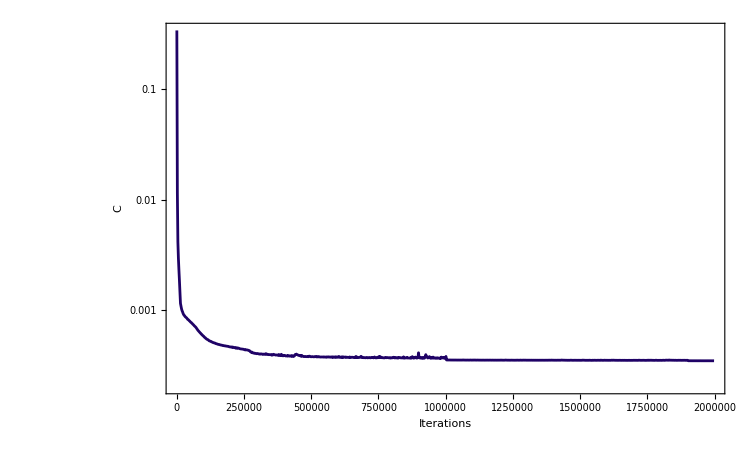

```mathematica
roundloss1=MapThread[List,{Range[Length@results1["RoundLossList"]],(*LowpassFilter[#,0.1]&@*)results1["RoundLossList"]}];
roundloss2=MapThread[List,{Range[Length@results2["RoundLossList"]],(*LowpassFilter[#,0.1]&@*)results2["RoundLossList"]}];
roundloss3=MapThread[List,{Range[Length@results3["RoundLossList"]],(*LowpassFilter[#,0.1]&@*)results3["RoundLossList"]}];
minposition1=roundloss1[[-1,1]];(*MinimalBy[roundloss1,#[[2]]&][[1,1]];*)
minposition2=minposition1+roundloss2[[-1,1]];(*+MinimalBy[roundloss2,#[[2]]&][[1,1]];*)
ListLogPlot[

{
Join[{{0,loss=Mean[untrainedNet[manifold,TargetDevice->"GPU",WorkingPrecision->"Real64"]]}},{results1["BatchesPerRound"]#[[1]],#[[2]]}&/@roundloss1[[1;;minposition1;;1]],{results1["BatchesPerRound"]#[[1]],#[[2]]}&/@((#+{minposition1,0})&/@roundloss2[[1;;minposition2-minposition1;;1]]),
{results1["BatchesPerRound"]#[[1]],#[[2]]}&/@((#+{minposition2,0})&/@roundloss3)](*,
{results1["BatchesPerRound"]#[[1]],#[[2]]}&/@roundloss1[[minposition1;;-1]],{results1["BatchesPerRound"]#[[1]],#[[2]]}&/@((#+{minposition1,0})&/@roundloss2[[minposition2-minposition1;;-1]])*)},Frame->True,FrameLabel->{"Iterations","C"},LabelStyle->"Subtitle",PlotStyle->Directive[ColorData["BlueGreenYellow"][0](*,Dashing[{0.03,0.003}]*)],FrameStyle->Directive[Black,Large,FontFamily->"Times New Roman"]]/.Point->Line
```

```mathematica
(*Raw latent cloud i.e. application of the encoder to the manifold data*)
latentcloud=encoder[manifold];

(*calculate u,v bounding box*)
bounds=1.1RegionBounds[BoundingRegion[#[[1;;2]]&/@latentcloud]](*10% margin, but assuming the latent cloud encompasses {u,v}={0,0} *)
boundsize={bounds[[1,2]]-bounds[[1,1]],bounds[[2,2]]-bounds[[2,1]]}


(*For the sake of memory, it is recommended to undersample the inside of the cloud while keeping the points close to the boundary intact. Therefore, we sample the bounding box and keep the latentcloud points that are nearest to each point in the bounding box and we undersample by a factor of 10 the rest (i.e. the 'inside' of the latentcloud)*)
boundingboxpoints=Join[
Flatten[Table[{x,y,0},{x,bounds[[1,1]],bounds[[1,2]],0.1},{y,bounds[[2,1]],bounds[[2,2]],0.1}],1],
Flatten[Table[{x,y,manifold[[-1,4]]+1},{x,bounds[[1,1]],bounds[[1,2]],0.1},{y,bounds[[2,1]],bounds[[2,2]],0.1}],1],
Flatten[Table[{-1,y,z},{y,bounds[[2,1]],bounds[[2,2]],0.1},{z,0,manifold[[-1,4]]+1,0.1}],1],
Flatten[Table[{1,y,z},{y,bounds[[2,1]],bounds[[2,2]],0.1},{z,0,manifold[[-1,4]]+1,0.1}],1],
Flatten[Table[{x,-1,z},{x,bounds[[1,1]],bounds[[1,2]],0.1},{z,0,manifold[[-1,4]]+1,0.1}],1],
Flatten[Table[{x,1,z},{x,bounds[[1,1]],bounds[[1,2]],0.1},{z,0,manifold[[-1,4]]+1,0.1}],1]
];
nearfun=Nearest[latentcloud];
latentcloud=Join[Flatten[nearfun[boundingboxpoints],1],latentcloud[[1;;-1;;10]],Flatten[nearfun[boundingboxpoints],1]];

latentcentroid=Mean[latentcloud];
```

{{-0.963275,0.984215},{-0.972323,1.10963}}

{1.94749,2.08195}

```mathematica
latentcloud[[-1]]
```

{0.566105,0.666952,10.685}

```mathematica
tmax*(2compressionfactor)
```

6.435

```mathematica
(*Create and visualise the latent alpha shape with ball radius α specified below. The t̃ time is temporarily rescaled by compressionfactor to sqeeze the latent surfaces (visualised in black) close together. The 2 in front of compressionfactor in the code below comes from the fact that t̃=t/(2timepscan) and visualise the plot in u,v,t̃ while adjusting the aspect ratio of the plot such that the ball appears spherical*)
α=0.3
compressionfactor=0.3;

compressedalphashape=ConcaveHullMesh[#{1,1,compressionfactor}&/@latentcloud[[1;;-1;;2]],α];
(*Uncompress the region*)
alphashape=BoundaryMesh[MeshRegion[({1,1,1/(compressionfactor)}#&/@MeshCoordinates[#]),MeshCells[#,3]]&@compressedalphashape];
tmax=Max[latentcloud[[All,3]]];

Show[{ListPointPlot3D[latentcloud[[1;;-1;;10]],PlotStyle->{Black,PointSize[0.01]},Lighting->{"Neutral",AmbientLight[GrayLevel[0.5]]},PlotRange->{{bounds[[1,1]],bounds[[1,2]]},{bounds[[2,1]],bounds[[2,2]]},{0,tmax}},AxesLabel->(Style[#,Directive[Black,Italic,36,FontFamily->"CMU Serif"]]&/@{"ũ","ṽ","t̃"})],
Graphics3D[{EdgeForm[Darker@Red],Red,Opacity[0.3],alphashape}],
(*Graphics3D[{Lighter@Lighter@Blue,Lighting->{"Neutral",AmbientLight[GrayLevel[0.5]]},Hyperplane[{0,0,1},{0,0,9}]}],*)
Graphics3D[Ellipsoid[{0.7,0.7,6},{α,α,α*(tmax*(compressionfactor))}]]
},BoxRatios->{boundsize[[1]],boundsize[[2]],tmax*(compressionfactor)}(*,ViewPoint->5{0.7,-1,0.3}*),

ViewProjection->"Orthographic",Ticks->{{-1,0,1},{-1,0,1},{0,4,8,12,16,20,24}},AxesEdge->{{0,0},{1,0},{1,1}},LabelStyle->Directive[25,FontFamily->"Times New Roman"],Lighting->"ThreePoint",ViewVertical->{0, 0, 1},ViewPoint->{0.5,-1,0.5},Lighting->{"Neutral",AmbientLight[GrayLevel[0.5]]}]
```

0.3

-Graphics3D-

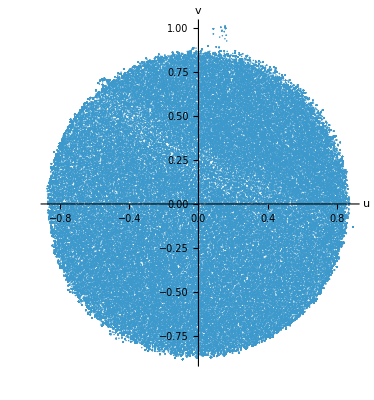

```mathematica
Show[{ListPlot[{1,1}#[[1;;2]]&/@latentcloud,PlotRange->All,AspectRatio->Automatic,AxesLabel->(Style[#,Directive[Black,Large,FontFamily->"MathJax_Math"]]&/@{"u","v"})],
Graphics[Circle[{0,0},1/rescale]]}]
```

```mathematica
(*Define a new non-trainable 'neural net' called GrandCompute which imports the trained decoder, but for each input {u,v,t̃} it outputs the following information:
{u,v,t̃}, 
{x,y,z,t}, 
principal curvatures κ1 and κ2, 
principal directions of curvature as vectors in the {x,y,z} space, 
the slopes du/dv of principal directions of curvature in the latent u-v space, 
the Christoffel symbols, 
the metric tensor 
and 
the jacobian. 
By implementing these computations as a neural network, we can execute them in a massively parallelized way on a GPU. 
The output of GrandCompute is flat and contains 34 elements for each {u,v,t̃} point, so it needs to be grouped together by enclosing GrandCompute[list of {u,v,t̃} points] with fixgroupoutput function.
*)

(*define the finite difference step*)
Delta=0.0001;
latentvicinitynet=NetChain[{FunctionLayer[
{{#[[1]],#[[2]],#[[3]]},
{#[[1]]+Delta,#[[2]],#[[3]]},
{#[[1]]-Delta,#[[2]],#[[3]]},
{#[[1]],#[[2]]+Delta,#[[3]]},
{#[[1]],#[[2]]-Delta,#[[3]]},

{#[[1]]+Delta,#[[2]]+Delta,#[[3]]},
{#[[1]]-Delta,#[[2]]+Delta,#[[3]]},
{#[[1]]+Delta,#[[2]]-Delta,#[[3]]},
{#[[1]]-Delta,#[[2]]-Delta,#[[3]]},

{#[[1]]+2Delta,#[[2]],#[[3]]},
{#[[1]]-2Delta,#[[2]],#[[3]]},
{#[[1]],#[[2]]+2Delta,#[[3]]},
{#[[1]],#[[2]]-2Delta,#[[3]]}
}&]}];

euvnet=FunctionLayer[{((#[[2]]-#[[3]])/(2Delta)),((#[[4]]-#[[5]])/(2Delta))}&];
metrictensornet=FunctionLayer[{{#[[1]].#[[1]],#[[1]].#[[2]]},{#[[1]].#[[2]],#[[2]].#[[2]]}}&];
accelerationlayer=FunctionLayer[{{((#[[10]]-2#[[1]]+#[[11]])/(2Delta)^2),((#[[6]]-#[[7]]-#[[8]]+#[[9]])/(2Delta)^2)},
{((#[[6]]-#[[8]]-#[[7]]+#[[9]])/(2Delta)^2),((#[[12]]-2#[[1]]+#[[13]])/(2Delta)^2)}
}&,"Input"->{13,3}];
christoff=FunctionLayer[{
{(#E[[1]])/(#E[[1]].#E[[1]]),(#E[[2]])/(#E[[2]].#E[[2]])}.#A[[1,1]],
{(#E[[1]])/(#E[[1]].#E[[1]]),(#E[[2]])/(#E[[2]].#E[[2]])}.#A[[1,2]],
{(#E[[1]])/(#E[[1]].#E[[1]]),(#E[[2]])/(#E[[2]].#E[[2]])}.#A[[2,1]],
{(#E[[1]])/(#E[[1]].#E[[1]]),(#E[[2]])/(#E[[2]].#E[[2]])}.#A[[2,2]]
}&,NetPort["E"]->{2,3},NetPort["A"]->{2,2,3}];
christoffelnet=NetGraph[{accelerationlayer,christoff},{NetPort["decodedvicinity"]->1->NetPort[{2,"A"}],NetPort["jacobian"]->NetPort[2,"E"]}];
rescalingmagnif1=rescalingmagnif[[1]];
rescalingmagnif2=rescalingmagnif[[2]];
rescalingmagnif3=rescalingmagnif[[3]];
rescalingmagnif4=rescalingmagnif44=rescalingmagnif444=rescalingmagnif4444=N@rescalingmagnif[[4]];

centroid1=centroid[[1]];
centroid2=centroid[[2]];
centroid3=centroid[[3]];
centroid4=N@centroid[[4]];
xvel=D[xtranslation[x],x];
yvel=D[ytranslation[y],y];
zvel=D[ztranslation[z],z];




decnet=NetGraph[<|
"decoder"->decoder,
"dec"->FunctionLayer[
(((#*{rescalingmagnif1,rescalingmagnif2,rescalingmagnif3,rescalingmagnif4})+{centroid1,centroid2,centroid3,centroid4}+
{xtranslation[#[[4]]*rescalingmagnif44+centroid4],
ytranslation[#[[4]]*rescalingmagnif444+centroid4],
ztranslation[#[[4]]*rescalingmagnif4444+centroid4],0}))[[1;;3]]&
]
|>,{NetPort["Input"]->"decoder"->"dec"}];
GrandCompute=NetGraph[<|
"latentvicinity"->latentvicinitynet,
"decout"->{decnet,FlattenLayer[]},
"decodedvicinity"->NetMapOperator[decnet],
"jacobian"->euvnet,
"jacobianflat"->FlattenLayer[],
"metrictensor"->{metrictensornet,FlattenLayer[]},
"christoffel"->{christoffelnet,FlattenLayer[]},

"d0d1d2"->FunctionLayer[{
Det[{(#[[2]]+#[[3]]-2#[[1]])/Delta^2,((#[[2]]-#[[3]])/(2Delta)),((#[[4]]-#[[5]])/(2Delta))}],
Det[{(1/(4 Delta^2))(#[[6]]+#[[9]]-#[[8]]-#[[7]]),((#[[2]]-#[[3]])/(2Delta)),((#[[4]]-#[[5]])/(2Delta))}],
Det[{(1/Delta^2)(#[[5]]+#[[5]]-2#[[1]])[[1;;3]],((#[[2]]-#[[3]])/(2Delta))[[1;;3]],((#[[4]]-#[[5]])/(2Delta))[[1;;3]]}]
}&,"Input"->{13,3}],

"EFG"->FunctionLayer[{Norm[((#[[2]]-#[[3]])/(2Delta))]^2,
((#[[2]]-#[[3]])/(2Delta)).((#[[4]]-#[[5]])/(2Delta)),
Norm[((#[[4]]-#[[5]])/(2Delta))]^2}&,"Input"->{13,3}],

"Ddenominator"->FunctionLayer[Sqrt[#[[1]]*#[[3]]-#[[2]]^2]&,"Input"->3],

"D0D1D2"->FunctionLayer[#d0d1d2/#Ddenominator&,NetPort["d0d1d2"]->{3}],

"curvatures"->FunctionLayer[{1/((#D[[3]] #EFG[[1]]-2 #D[[2]] #EFG[[2]]+#D[[1]] #EFG[[3]]+√((-#D[[3]] #EFG[[1]]+2 #D[[2]] #EFG[[2]]-#D[[1]] #EFG[[3]])^2-4 (-(#D[[2]])^2+#D[[1]] #D[[3]]) (-(#EFG[[2]])^2+#EFG[[1]] #EFG[[3]])))/(2 (-(#D[[2]])^2+#D[[1]] #D[[3]]))),
1/((#D[[3]] #EFG[[1]]-2 #D[[2]] #EFG[[2]]+#D[[1]] #EFG[[3]]-√((-#D[[3]] #EFG[[1]]+2 #D[[2]] #EFG[[2]]-#D[[1]] #EFG[[3]])^2-4 (-(#D[[2]])^2+#D[[1]] #D[[3]]) (-(#EFG[[2]])^2+#EFG[[1]] #EFG[[3]])))/(2 (-(#D[[2]])^2+#D[[1]] #D[[3]])))}&,NetPort["D"]->3,NetPort["EFG"]->3],


"principaldirectionslatent"->FunctionLayer[{(#D[[3]] #EFG[[1]]-#D[[1]] #EFG[[3]]+√((-#D[[3]] #EFG[[1]]+#D[[1]] #EFG[[3]])^2-4 (-#D[[2]] #EFG[[1]]+#D[[1]] #EFG[[2]]) (-#D[[3]] #EFG[[2]]+#D[[2]] #EFG[[3]])))/(2 (-#D[[3]] #EFG[[2]]+#D[[2]] #EFG[[3]])),
(#D[[3]] #EFG[[1]]-#D[[1]] #EFG[[3]]-√((-#D[[3]] #EFG[[1]]+#D[[1]] #EFG[[3]])^2-4 (-#D[[2]] #EFG[[1]]+#D[[1]] #EFG[[2]]) (-#D[[3]] #EFG[[2]]+#D[[2]] #EFG[[3]])))/(2 (-#D[[3]] #EFG[[2]]+#D[[2]] #EFG[[3]]))}&,NetPort["D"]->3,NetPort["EFG"]->3],


"principaldirectionsxyz"->NetGraph[{FunctionLayer[{#uvt,#uvt+{0.001/(√(1+#princ[[1]]^2)),(#princ[[1]]*0.001)/(√(1+#princ[[1]]^2)),0},#uvt+{0.001/(√(1+#princ[[2]]^2)),(#princ[[2]]*0.001)/(√(1+#princ[[2]]^2)),0}}&,

NetPort["uvt"]->3,NetPort["princ"]->2],NetMapOperator[decnet],FunctionLayer[{(#[[2]]-#[[1]])/0.001,(#[[3]]-#[[1]])/0.001}&],FlattenLayer[]},{1->2->3->4}],

"Out"->CatenateLayer[]

|>,{NetPort["Input"]->"latentvicinity"->"decodedvicinity"->"jacobian"->NetPort["christoffel","jacobian"],"decodedvicinity"->NetPort["christoffel","decodedvicinity"],
"decodedvicinity"->{"d0d1d2","EFG"},

"d0d1d2"->NetPort["D0D1D2","d0d1d2"],"EFG"->"Ddenominator"->NetPort["D0D1D2","Ddenominator"],
"D0D1D2"->NetPort["curvatures","D"],"EFG"->NetPort["curvatures","EFG"],
"D0D1D2"->NetPort["principaldirectionslatent","D"],"EFG"->NetPort["principaldirectionslatent","EFG"],
NetPort["Input"]->NetPort["principaldirectionsxyz","uvt"],"principaldirectionslatent"->NetPort["principaldirectionsxyz","princ"],
"jacobian"->"metrictensor",

NetPort["Input"]->"Out",
"decout"->"Out",
"curvatures"->"Out",
"principaldirectionsxyz"->"Out",
"principaldirectionslatent"->"Out",

"christoffel"->"Out",
"metrictensor"->"Out",
"jacobian"->"jacobianflat"->"Out"

}];
Clear[fixgroupoutput];


fixgroupoutput[list_]:={{#[[1]],#[[2]],#[[3]]}(*1 uv t̃*),
Append[#[[4;;6]],#[[3]]*rescalingmagnif4444+centroid4](*2 xyzt*),
If[Abs[#[[7]]]>Abs[#[[8]]],#[[{8,7}]],#[[7;;8]]](*3 κ1κ2*),
If[Abs[#[[7]]]>Abs[#[[8]]],{#[[12;;14]],#[[9;;11]]},{#[[9;;11]],#[[12;;14]]}](*4 principalxyz*),
#[[15;;16]](*5 du/dv slopes of principal direction of curvature*),
{#[[17;;18]],#[[19;;20]],#[[21;;22]],#[[23;;24]]}(*6 Christoffel Symbols*),
{#[[25;;26]],#[[27;;28]]}(*7 metric tensor g*),
{#[[29;;31]],#[[32;;34]]}(*8 jacobian*)}&/@list;
```

```mathematica
(*COMPUTE THE OUTPUT here for a list of moments in t̃ specified below by sampling the u,v plane with resolution specified by ures and vres.
The first viable moment in time is the time-coordinate of the point scanned last in the first scan. 
Below we provide an example list of sampling times, but the user may choose a different one *)

sampletimes=Range[(timepscan-centroid4)/rescalingmagnif4,tmax-timepscan/rescalingmagnif4,0.5];

Monitor[latentsurfaces=Table[
time=sampletimes[[ii]];
(*latentsliceregion=UnitDisk=DelaunayMesh[1/rescale Join[Flatten[Table[If[{u,v}∈Disk[],{u,v},Nothing],{u,-1,1,0.02},{v,-1,1,0.02}],1],CirclePoints[200]]];
*)
ures=140;
vres=140;
latentpoints=Flatten[Table[If[{u,v,time}∈alphashape,{u,v},Nothing],{u,bounds[[1,1]],bounds[[1,2]],boundsize[[1]]/ures},{v,bounds[[2,1]],bounds[[2,2]],boundsize[[2]]/vres}],1];
latentpointscentroid=Mean[latentpoints];
boundaryspline=BSplineFunction[(latentpointscentroid[[1;;2]]+(1+(2Mean[boundsize/{ures,vres}])/(Mean[boundsize]/2.2))(#-latentpointscentroid[[1;;2]]))&/@(meshboundarycoords=SortBy[MeshCoordinates[RegionBoundary[ConcaveHullMesh[latentpoints,0.1]]],ArcTan[#[[1]]-latentpointscentroid[[1]],#[[2]]-latentpointscentroid[[2]]]&]),SplineClosed->True,SplineDegree->Length[meshboundarycoords]];
boolregionlatent=BoundaryMeshRegion@Polygon[Table[boundaryspline[s],{s,0,1,0.01}]];
Show[{ParametricPlot[boundaryspline[s],{s,0,1}]
,latentsliceregion=ConcaveHullMesh[latentpointsrefined=Flatten[Table[If[{u,v}∈boolregionlatent,{u,v},Nothing],{u,bounds[[1,1]],bounds[[1,2]],boundsize[[1]]/ures},{v,bounds[[2,1]],bounds[[2,2]],boundsize[[2]]/vres}],1],0.1]}];


{#[[1]],#[[2]],time}&/@MeshCoordinates[latentsliceregion](*latentsliceregion*),{ii,Length@sampletimes}];,{ii}]


Monitor[granddata=Table[fixgroupoutput@GrandCompute[latentsurfaces[[i]],TargetDevice->"GPU",WorkingPrecision->"Real64"],{i,Length@latentsurfaces}];,i];


out={0,
Mean@Flatten[granddata[[All,All,3,2]],1],
Mean[Abs@Flatten[granddata[[All,All,3,1]],1]],
Mean[Abs@Flatten[granddata[[All,All,3,1]]*granddata[[All,All,3,2]],1]]}
```

{0,82.7489,5.67686,2458.13}

```mathematica
(*Plot the output, here for the times of sampletimes[[1,3,5,7,9]]*)
Show[Table[Show[{Graphics3D[{MaterialShading[{"Clay",Blend[{ColorData["BlueGreenYellow"][0.2(*granddata[[no,1,2,4]]/(hypercloud[[-1,-1,4]]-hypercloud[[1,1,4]])*)],GrayLevel[0.8]},0.4]}],
mesh=MeshRegion[granddata[[no,All,2,1;;3]],MeshCells[ConcaveHullMesh[granddata[[no,All,1,1;;2]]],2]]
},Lighting->{"Neutral",AmbientLight[GrayLevel[0.5]]}],
(*Highlight the outline as a red tube*)
Graphics3D[{Red,Tube[decnet[{#[[1]],#[[2]],granddata[[no,1,1,3]]}&/@SortBy[MeshCoordinates[RegionBoundary[ConcaveHullMesh[granddata[[no,All,1,1;;2]],α]]],ArcTan[#[[1]],#[[2]]]&],TargetDevice->"GPU"],0.011*rescalingmagnif1]}],
(*The two tables below generate the grid of lines of constant u and v*)
Table[Graphics3D[{Black,Tube[BSplineCurve@Table[If[{u,v,granddata[[no,1,1,3]]}∈alphashape,decnet[{u,v,granddata[[no,1,1,3]]}][[1;;3]],Nothing],{u,bounds[[1,1]]/1.1,bounds[[1,2]]/1.1,0.01}],0.005*rescalingmagnif1]}],{v,bounds[[2,1]]/1.1,bounds[[2,2]]/1.1,0.1}],
Table[Graphics3D[{Black,Tube[BSplineCurve@Table[If[{u,v,granddata[[no,1,1,3]]}∈alphashape,decnet[{u,v,granddata[[no,1,1,3]]}][[1;;3]],Nothing],{v,bounds[[2,1]]/1.1,bounds[[2,2]]/1.1,0.01}],0.005*rescalingmagnif1]}],{u,bounds[[1,1]]/1.1,bounds[[1,2]]/1.1,0.1}]



}],{no,{1,3,5,7,9}}],Boxed->True,ViewProjection->"Orthographic",Axes->True,AxesEdge->{{0,0},{0,0},{0,1}},ViewPoint->{-1,-0.4,0.5},ViewVertical->{0, 0, 1},AxesStyle->Directive[Black,Large,FontFamily->"Times"]]
```

-Graphics3D-

```mathematica
(*The area of the sheet in the demo is π*0.019^2=0.001134)
```

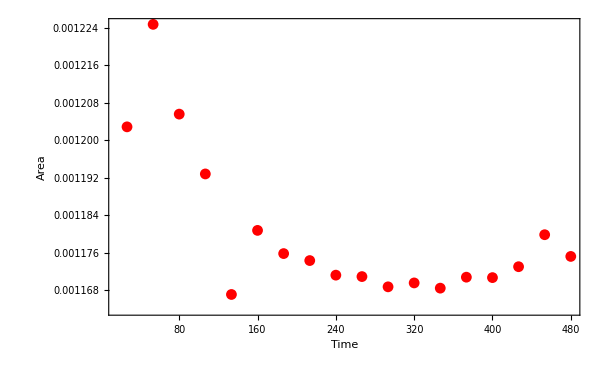

```mathematica
(*Plot the area of the reconstructed meshes*)
ListPlot[Table[{granddata[[no,1,2,4]],Area@MeshRegion[granddata[[no,All,2,1;;3]],MeshCells[ConcaveHullMesh[granddata[[no,All,1,1;;2]]],2]]},{no,1,Length@granddata}],Frame->True,FrameLabel->{"Time","Area"},PlotRange->All,PlotStyle->Red,LabelStyle->Directive[Black,Large,FontFamily->"Times New Roman"]]
```